```mathematica
SymbolReplace[sym_,edge_]:=Block[{s},
s=SymbolToSets[sym];
s=Map[Sort[Flatten[(#/.edge[[1]]->{edge[[1]],edge[[2]]})]]&,s];
SetsToSymbol[s]
]
```

```mathematica
JoinGraphs[f_,g_,h_]:=Block [{edges,full},
edges=Join[
Table[e->Directive[{Thick,Red}],{e,EdgeList[f]}],
Table[e->Directive[{Thick,Yellow}],{e,SetDifference[SetDifference[EdgeList[g],EdgeList[f]],EdgeList[h]]}],
Table[e->Directive[{Thick,Blue}],{e,EdgeList[h]}]
];
full=GraphUnion[f,g,h];
Graph[full,VertexLabels->Table[v->If[SymbolLevel[v]==4,Rotate[Framed[SymbolToLabel[v],FrameStyle->Directive[Red,Thin]],Pi/6],Rotate[SymbolToLabel[v],Pi/6]],{v,VertexList[full]}],EdgeStyle->edges,
VertexStyle->Join[
Table[v->Red,{v,VertexList[f]}],
Table[v->Blue,{v,VertexList[h]}]],
GraphLayout->"LayeredDigraphEmbedding",
ImageSize->400
]
]
```

```mathematica
FindFullFormula12345[g_]:=Block[{},
Monitor[
formulaDepth=0;FindFullFormula12345[g,Table[{v},{v,VertexList[g]}]],
formulaDepth
]
]
```

```mathematica
FindFullFormula12345[g_,v_]:=Block[{edge,pos1,pos2,v2,result={},result1,result2,clique},
If[CompleteGraphQ[g],
result=Select[{SetsToSymbol2[Sort[Map[Sort[#]&,v],#1[[1]]<#2[[1]]&]]},SymbolLevel[#]≤5&]
,
clique=First[FindClique[g]];
If[Length[clique]≤5,
edge=First[EdgeList[GraphComplement[g]]];
Table[If[MemberQ[v[[k]],edge[[1]]],pos1=k],{k,Length[v]}];
Table[If[MemberQ[v[[k]],edge[[2]]],pos2=k],{k,Length[v]}];
v2=v;
v2[[pos1]]=Join[v2[[pos1]],v2[[pos2]]];
v2=Delete[v2,pos2];
result=Join[
FindFullFormula12345[EdgeAdd[g,edge],v],
FindFullFormula12345[VertexContract[g,{edge[[1]],edge[[2]]}],v2]
]
,
{}
]
];
If[Length[result]>formulaDepth,formulaDepth=Length[result]];
result
]
```

```mathematica
HandleGraph[g_]:=Block[{edges,full},
edges=DeleteDuplicates[EdgeList[g],IsomorphicGraphQ[EdgeContract[g,#1],EdgeContract[g,#2]]&];
Monitor[
Graph[g,VertexLabels->"Name"]->
Table[With[{
without=Graph[EdgeDelete[g,e],VertexLabels->"Name",GraphHighlight->{e[[1]],e[[2]]},GraphHighlightStyle->"Thick",GraphLayout->"TutteEmbedding"],
contract =Graph[EdgeContract[g,e],VertexLabels->"Name",GraphHighlight->{e[[1]]},GraphHighlightStyle->"Thick",GraphLayout->"TutteEmbedding"],
with=Graph[g,GraphHighlight->e,GraphLayout->"TutteEmbedding", VertexLabels->"Name",GraphHighlightStyle->"Thick"]
},
Labeled[
Graph[
JoinGraphs[
FormulaGraphReverse2[FindFullFormula[g]],
FormulaGraphReverse2[FindFullFormula[without]],
FormulaGraphReverse2[Map[SymbolReplace[#,e]&,FindFullFormula[contract]]]
],ImageSize->800
],
{
e,
Yellow->{"Without",ChromaticPolynomial[without,4]/24,without},
"==",
Red->{"With",ChromaticPolynomial[g,4]/24,with},
Blue->{"Contract",ChromaticPolynomial[contract,4]/24,contract}
}
]
],{e,edges}],
e]
]
```

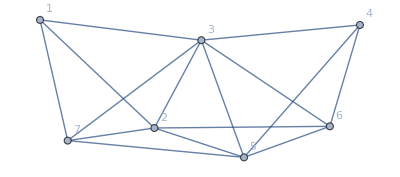
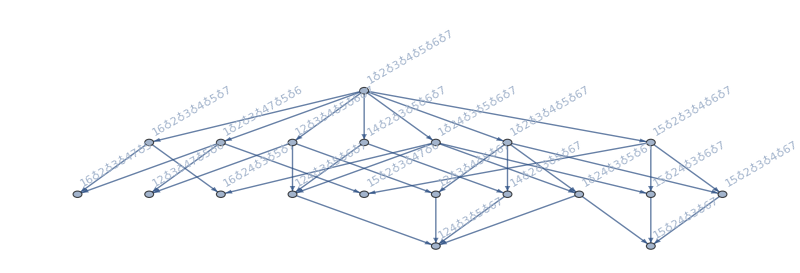
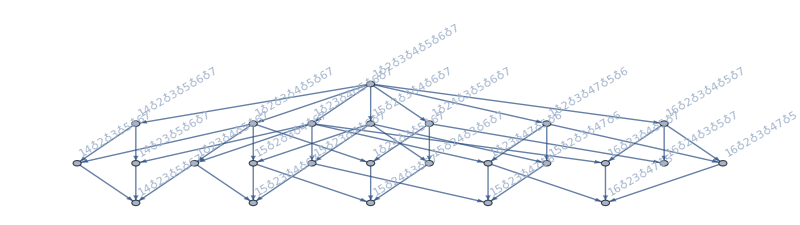
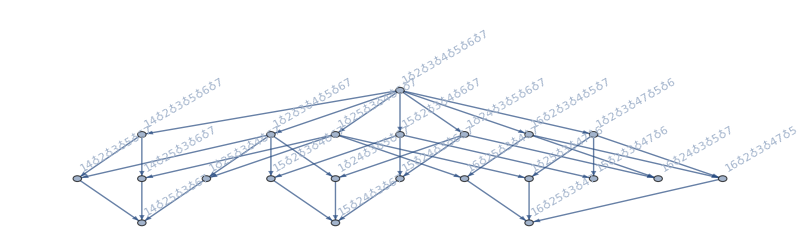
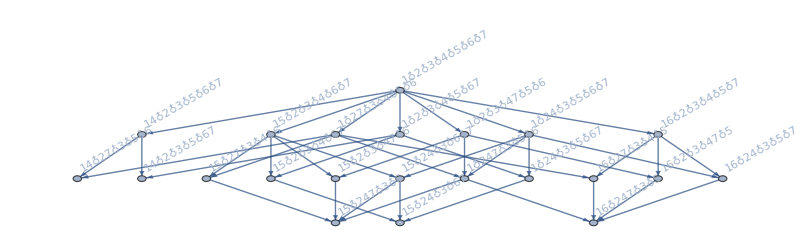
-Graphics-→{-Graphics-{1<->2,RGBColor[1, 1, 0]→{Without,2,-Graphics-},==,RGBColor[1, 0, 0]→{With,1,-Graphics-},RGBColor[0, 0, 1]→{Contract,1,-Graphics-}},-Graphics-{2<->3,RGBColor[1, 1, 0]→{Without,5,-Graphics-},==,RGBColor[1, 0, 0]→{With,1,-Graphics-},RGBColor[0, 0, 1]→{Contract,4,-Graphics-}},-Graphics-{2<->5,RGBColor[1, 1, 0]→{Without,3,-Graphics-},==,RGBColor[1, 0, 0]→{With,1,-Graphics-},RGBColor[0, 0, 1]→{Contract,2,-Graphics-}},-Graphics-{2<->7,RGBColor[1, 1, 0]→{Without,3,-Graphics-},==,RGBColor[1, 0, 0]→{With,1,-Graphics-},RGBColor[0, 0, 1]→{Contract,2,-Graphics-}}}

```mathematica
HandleGraph[ReadGrof[5]]
```

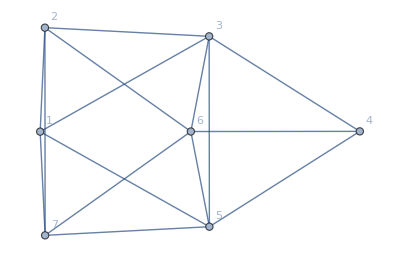
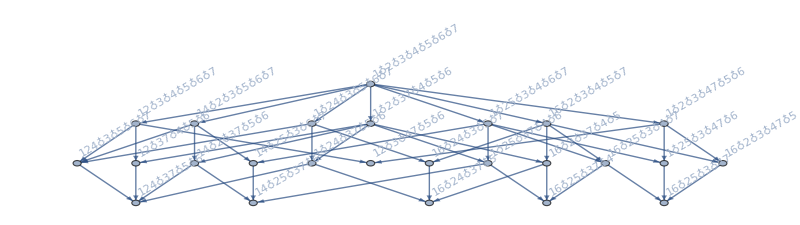
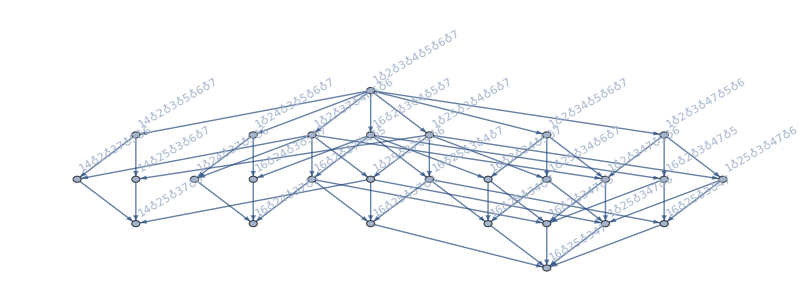
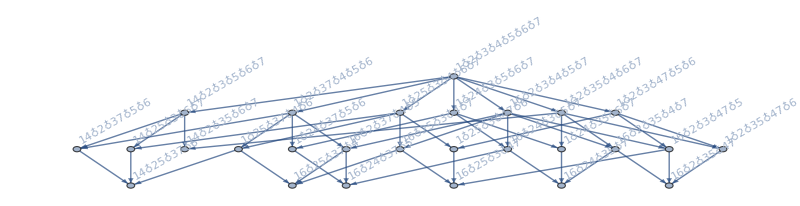
-Graphics-→{-Graphics-{1<->2,RGBColor[1, 1, 0]→{Without,5,-Graphics-},==,RGBColor[1, 0, 0]→{With,4,-Graphics-},RGBColor[0, 0, 1]→{Contract,1,-Graphics-}},-Graphics-{3<->4,RGBColor[1, 1, 0]→{Without,8,-Graphics-},==,RGBColor[1, 0, 0]→{With,4,-Graphics-},RGBColor[0, 0, 1]→{Contract,4,-Graphics-}},-Graphics-{3<->5,RGBColor[1, 1, 0]→{Without,6,-Graphics-},==,RGBColor[1, 0, 0]→{With,4,-Graphics-},RGBColor[0, 0, 1]→{Contract,2,-Graphics-}}}

```mathematica
HandleGraph[ReadGrof[6]]
```

```mathematica
Monitor[
Table[
HandleGraph[ReadGrof[k]],
{k,5,12}
],k]
```

```mathematica
Table[
Map[SymbolLevel,l]//Tally//Sort,
{l,{{v1x2x3x4x5x6x7,v1x2x3x47x5x6,v1x2x3x4x5x67,v1x24x3x5x6x7,v1x24x3x5x67,v14x2x3x5x6x7,v14x2x3x5x67,v16x2x3x4x5x7,v16x2x3x47x5,v16x24x3x5x7,v15x2x3x4x6x7,v15x2x3x47x6,v15x2x3x4x67,v15x24x3x6x7,v15x24x3x67},{v1x2x3x4x5x6x7,v1x2x3x47x5x6,v1x2x3x4x5x67,v1x24x3x5x6x7,v1x24x3x5x67,v1x27x3x4x5x6,v1x247x3x5x6,v14x2x3x5x6x7,v14x2x3x5x67,v14x27x3x5x6,v16x2x3x4x5x7,v16x2x3x47x5,v16x24x3x5x7,v16x27x3x4x5,v16x247x3x5,v15x2x3x4x6x7,v15x2x3x47x6,v15x2x3x4x67,v15x24x3x6x7,v15x24x3x67,v15x27x3x4x6,v15x247x3x6},{v1x27x3x4x5x6,v1x274x3x5x6,v14x27x3x5x6,v16x27x3x4x5,v16x274x3x5,v15x27x3x4x6,v15x274x3x6},{v1x2x3x4x5x6,v1x24x3x5x6,v14x2x3x5x6,v16x2x3x4x5,v16x24x3x5,v15x2x3x4x6,v15x24x3x6}}}
]//Column
```

{{4,1},{5,7},{6,6},{7,1}}
{{4,3},{5,11},{6,7},{7,1}}
{{4,2},{5,4},{6,1}}
{{4,2},{5,4},{6,1}}

```mathematica
Map[{SymbolLevel[#],#}&,{v1x2x3x4x5x6x7,v1x2x3x47x5x6,v1x2x3x4x5x67,v1x24x3x5x6x7,v1x24x3x5x67,v1x27x3x4x5x6,v1x247x3x5x6,v14x2x3x5x6x7,v14x2x3x5x67,v14x27x3x5x6,v16x2x3x4x5x7,v16x2x3x47x5,v16x24x3x5x7,v16x27x3x4x5,v16x247x3x5,v15x2x3x4x6x7,v15x2x3x47x6,v15x2x3x4x67,v15x24x3x6x7,v15x24x3x67,v15x27x3x4x6,v15x247x3x6}]//Sort
```

{{4,v15x247x3x6},{4,v15x24x3x67},{4,v16x247x3x5},{5,v14x27x3x5x6},{5,v14x2x3x5x67},{5,v15x24x3x6x7},{5,v15x27x3x4x6},{5,v15x2x3x47x6},{5,v15x2x3x4x67},{5,v16x24x3x5x7},{5,v16x27x3x4x5},{5,v16x2x3x47x5},{5,v1x247x3x5x6},{5,v1x24x3x5x67},{6,v14x2x3x5x6x7},{6,v15x2x3x4x6x7},{6,v16x2x3x4x5x7},{6,v1x24x3x5x6x7},{6,v1x27x3x4x5x6},{6,v1x2x3x47x5x6},{6,v1x2x3x4x5x67},{7,v1x2x3x4x5x6x7}}

```mathematica
ChromaticPolynomial[Graph[plantri[[1]]],3]
```

0